# Using Substitution Systems as a Model for Biological Growth

## How can string replacement model growth?

```mathematica
Clear[PlotLengths]
PlotLengths[l_List, ops:OptionsPattern[ListLinePlot]]:=Labeled[l,ListLinePlot[StringLength/@l, ops]]
```

## Concretely

### Types of Basic Reproduction

#### Asexual Reproduction with no outside influences:

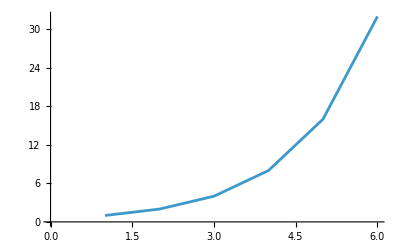
{A,AA,AAAA,AAAAAAAA,AAAAAAAAAAAAAAAA,AAAAAAAAAAAAAAAAAAAAAAAAAAAAAAAA}-Graphics-

```mathematica
SubstitutionSystem[{"A"->"AA"}, "A", 5]//PlotLengths
```

#### Asexual Reproduction with cycle time (e.g. young cells vs mature cells) :

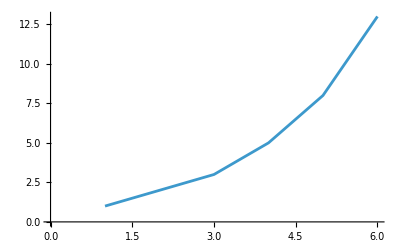
{A,AB,ABA,ABAAB,ABAABABA,ABAABABAABAAB}-Graphics-

```mathematica
SubstitutionSystem[{"A"->"AB", "B"->"A"}, "A", 5]//PlotLengths
```

#### Sexual Reproduction:

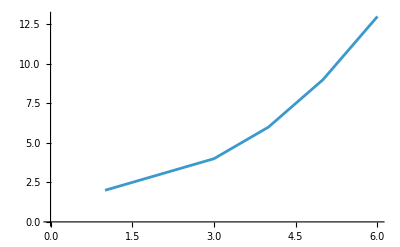
{AA,AAA,AAAA,AAAAAA,AAAAAAAAA,AAAAAAAAAAAAA}-Graphics-

```mathematica
SubstitutionSystem[{"AA"->"AAA"}, "AA", 5]//PlotLengths
```

#### Sexual Reproduction with cycle time:

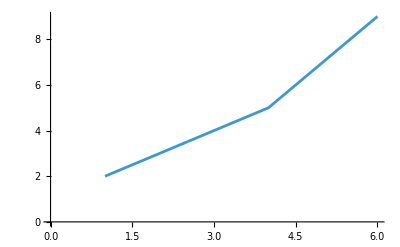
{AA,AAB,AABA,AABAA,AABAAAB,AABAAABAA}-Graphics-

```mathematica
SubstitutionSystem[{"AA"->"AAB", "B"->"A"}, "AA", 5]//PlotLengths
```

### Reproduction with Resource Constraints

Consider the problem of predator/prey interaction:
The prey repopulate at a rate proportional to their current population and are killed at a rate proportional to the predator population.
The predators repopulate at a rate proportional to their current population and proportional to the excess of predator to prey.

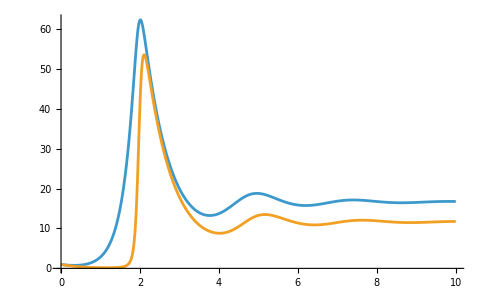

```mathematica
maxt=10;

s=NDSolve[{
x'[t]==3.5x[t]-5y[t],
y'[t]==2((x[t]-y[t])/5 - 1)y[t],
x[0]==y[0]==1
},{x,y},{t,maxt}];

Plot[Evaluate[{x[t],y[t]}/.s],{t,0,maxt}, PlotRange->All]
```

```mathematica
SubstitutionSystem[{"FFAA"->"FBAA", "F"->"FF","B"->"A"}, "FAA", 15]
```

{FAA,FFAA,FBAA,FFAAA,FBAAA,FFAAAA,FBAAAA,FFAAAAA,FBAAAAA,FFAAAAAA,FBAAAAAA,FFAAAAAAA,FBAAAAAAA,FFAAAAAAAA,FBAAAAAAAA,FFAAAAAAAAA}

But this is only linear. Why?
Because there is only one food-organism interface, and that’s the only place that organisms can reproduce.

```mathematica
RandomStringSubstitutionSystem[rules_, init_, steps_]:=NestList[StringReplace[#, RandomChoice[rules]]&, init, steps]
RandomWeightedStringSubstitutionSystem[wrules_, init_, steps_]:=NestList[StringReplace[#, RandomChoice[Rule@@Transpose[wrules]]]&, init, steps]
```

```mathematica
SeedRandom[2];
RandomStringSubstitutionSystem[{"F"->"FF", "FAA"->"AAB", "B"->"A"}, "FFAA", 15]
```

{FFAA,FFAA,FFAA,FFFFAA,FFFFAA,FFFAAB,FFFFFFAAB,FFFFFFAAA,FFFFFAABA,FFFFAABBA,FFFAABBBA,FFFFFFAABBBA,FFFFFAABBBBA,FFFFFAAAAAAA,FFFFAABAAAAA,FFFFFFFFAABAAAAA}

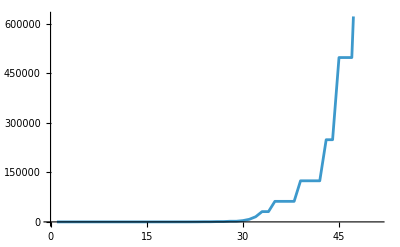

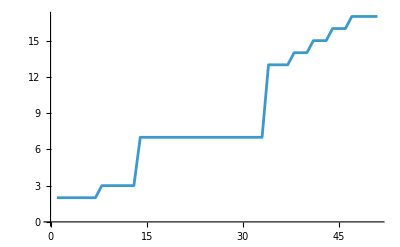

FFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFAABBAAAAA

```mathematica
SeedRandom[2];
PlotLengths[data=RandomStringSubstitutionSystem[{"F"->"FF", "FAA"->"AAB", "B"->"A"}, "FFAA", 50]][[2]]

ListLinePlot[data2=ParallelMap[StringCount[#, "A"]&,data]]

data[[20]]
```

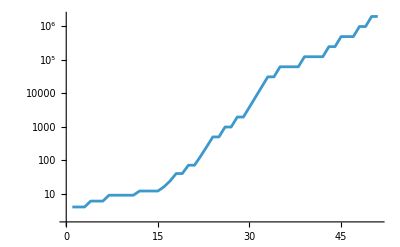

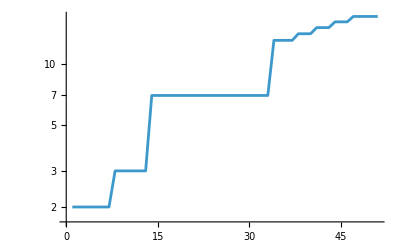

```mathematica
ListLogPlot[StringLength/@data, Joined->True]
ListLogPlot[data2, Joined->True]
```

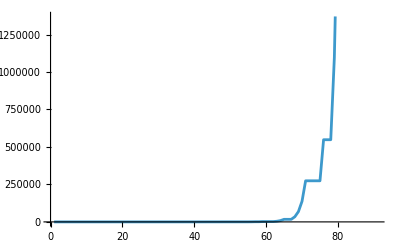

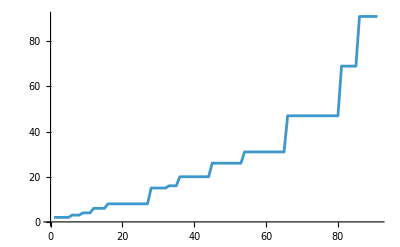

{FFFFAA,FFFAAB,FFFFFFAAB,FFFFFFAAB,FFFFFFAAB,FFFFFFAAA,FFFFFFAAA,FFFFFAABA,FFFFFAAAA,FFFFAABAA}

```mathematica
SeedRandom[4];

PlotLengths[data=RandomStringSubstitutionSystem[{"F"->"FF", "FAA"->"AAB", "B"->"A", "AAAA"->"AAAAF"}, "FFFFAA", 90]][[2]]

ListLinePlot[data2=ParallelMap[StringCount[#, "A"]&,data]]

data[[;;UpTo[10]]]
```

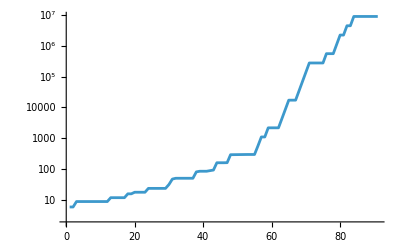

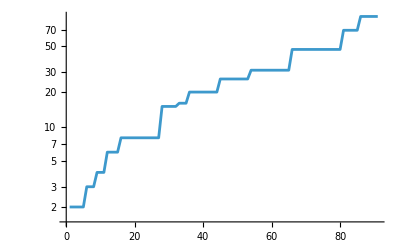

```mathematica
ListLogPlot[StringLength/@data, Joined->True]
ListLogPlot[data2, Joined->True]
```

### Sort of working balanced version

#### Try 1

```mathematica
First[ReverseSortBy[ParallelTable[SeedRandom[i]; i->Max[StringCount[#, "A"]&/@RandomWeightedStringSubstitutionSystem[{{1,"F"->"FF"},{10,"FF"->"FFF"},{50, "FFA"->"AA"}, {50, "AFF"->"AA"}, {50, "AF"->"FA"}, {50, "FA"->"AF"}, {5, "AAAAA"->"AAAA"}}, "FFFFFFFFA", 300]], {i, 100}],Last]]
```

37→59

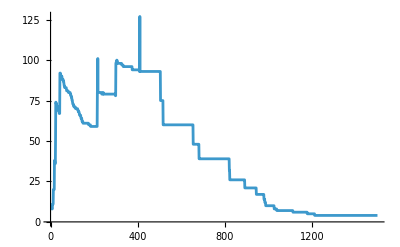

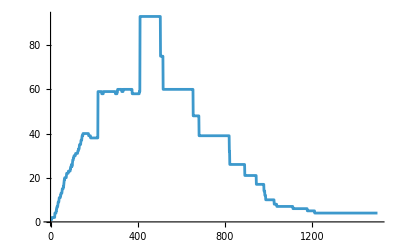

```mathematica
SeedRandom[37];

PlotLengths[data=RandomWeightedStringSubstitutionSystem[{{1,"F"->"FF"},{10,"FF"->"FFF"},{50, "FFA"->"AA"}, {50, "AFF"->"AA"}, {50, "AF"->"FA"}, {50, "FA"->"AF"}, {5, "AAAAA"->"AAAA"}}, "FFFFFFFFA", 1500]][[2]]

ListLinePlot[data2=ParallelMap[StringCount[#, "A"]&,data]]
```

#### Try 2

```mathematica
rule={{10, "AFA"->"AFFFA"},{2, "FF"->"FFF"},{50, "FFFFF"->"FFFFFF"},{50, "FFA"->"AA"}, {50, "AFF"->"AA"}, {50, "AF"->"FA"}, {50, "FA"->"AF"},{50, "AFF"->"FFA"}, {50, "FFA"->"AFF"}, {24, "AAA"->"AA"}};
init="FFFFFFFFA";
```

```mathematica
ReverseSortBy[ParallelTable[SeedRandom[i]; i->Max[StringCount[#, "A"]&/@RandomWeightedStringSubstitutionSystem[rule, init, 300]], {i, 200}],Last][[;;UpTo[50]]]
```

{41→37,88→35,137→26,180→24,196→22,80→18,133→17,161→14,51→14,149→13,62→12,105→11,83→11,78→11,59→11,45→11,44→11,30→11,142→10,31→10,24→10,6→10,165→9,113→9,107→9,93→9,194→8,182→8,178→8,173→8,164→8,125→8,124→8,121→8,28→8,22→8,16→8,171→7,163→7,153→7,152→7,148→7,141→7,136→7,130→7,127→7,126→7,106→7,99→7,85→7}

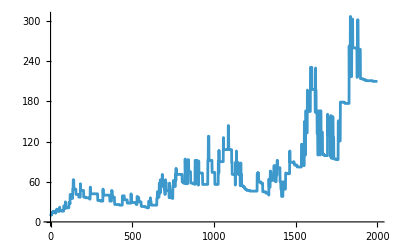

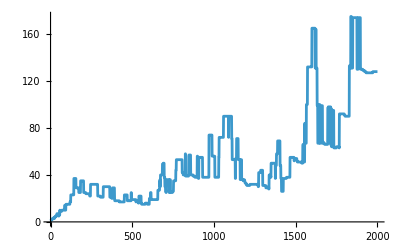

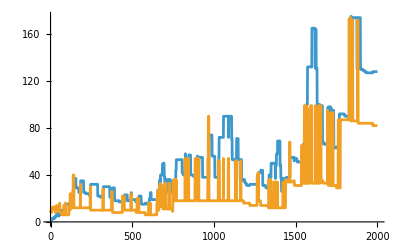

```mathematica
SeedRandom[First[First[]]];

PlotLengths[data=RandomWeightedStringSubstitutionSystem[rule, init, 2000]][[2]]

ListLinePlot[data2=ParallelMap[StringCount[#, "A"]&,data]]

ListLinePlot[{ParallelMap[StringCount[#, "A"]&,data], ParallelMap[StringCount[#, "F"]&,data]}]
```

#### Try 3

```mathematica
rule={{1, "AFA"->"AFFFA"}, {1, "FFF"->"FFFF"}, {1, "AAA"->"AA"}, {5, "FFA"->"FAA"}, {5, "FFA"->"AFF"}, {5, "AFF"->"FFA"}};
init="FFAA";
```

```mathematica
ReverseSortBy[ParallelTable[SeedRandom[i]; i->Max[StringCount[#, "A"]&/@RandomWeightedStringSubstitutionSystem[rule, init, 20]], {i, 500}],Last][[;;UpTo[50]]]
```

{112→8,466→7,215→7,179→7,165→7,437→6,300→6,282→6,273→6,212→6,208→6,86→6,479→5,465→5,371→5,324→5,228→5,213→5,178→5,152→5,130→5,83→5,62→5,48→5,32→5,30→5,15→5,473→4,457→4,453→4,438→4,422→4,388→4,375→4,361→4,356→4,354→4,345→4,305→4,293→4,283→4,260→4,259→4,252→4,224→4,197→4,169→4,161→4,144→4,131→4}

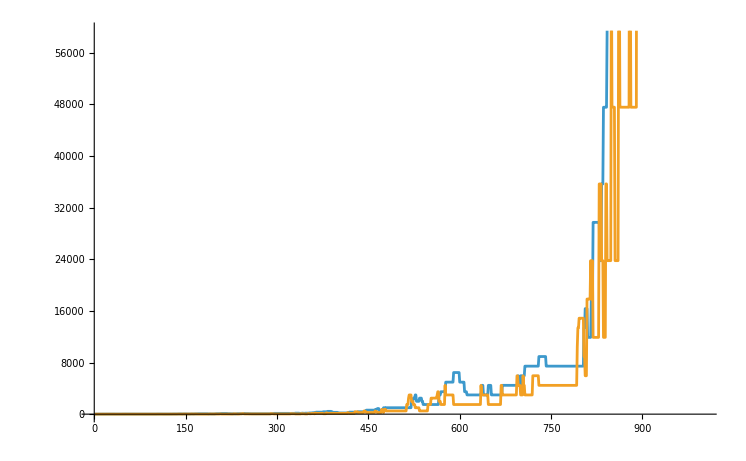

```mathematica
SeedRandom[112];

data=RandomWeightedStringSubstitutionSystem[rule, init,1000];

PlotLengths[data][[2]];

ListLinePlot[data2=ParallelMap[StringCount[#, "A"]&,data]];

ListLinePlot[{ParallelMap[StringCount[#, "A"]&,data], ParallelMap[StringCount[#, "F"]&,data]}]
```

### Abstract Concepts

#### Observed vs Actual Growth Behavior

Real growth is S-curved, not exponential.

#### Growth Classification

Generally, substitution systems
- grow arithmetically
- grow geometrically

For example,

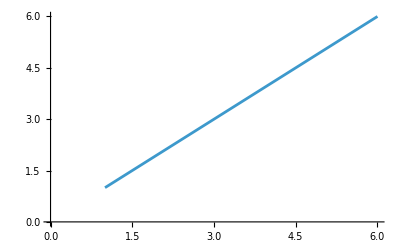
{A,BA,BBA,BBBA,BBBBA,BBBBBA}-Graphics-

{A,AA,AAAA,AAAAAAAA,AAAAAAAAAAAAAAAA,AAAAAAAAAAAAAAAAAAAAAAAAAAAAAAAA}-Graphics-

```mathematica
SubstitutionSystem[{"A"->"BA"}, "A", 5]//PlotLengths
SubstitutionSystem[{"A"->"AA"}, "A", 5]//PlotLengths
```

Cases like die-out can be modeled as an arithmetic delta of 0.

## How can we search for instances of that?

### MVP Code

### Optimization Ideas

```mathematica
NestList[#/.{x___, 0, 1, 0, y___}->{x, 1, 0, 1, y}, {
```